```mathematica
$HistoryLength=0;
(* Unifying all the scripts *)
Get["G:\\LAT\\sd_metropolis\\convergence_analysis.m"];
Get["G:\\LAT\\sd_metropolis\\apps\\pcm_wc_mspace\\pcm_wc_mspace_exact.m"];
Get["G:\\LAT\\sd_metropolis\\apps\\pcm_wc_mspace\\pcm_wc_mspace_analysis.m"];
(* Simulation parameters *)GetConvergenceSummary[LT_,LS_,λ_,mmax_,datadir_,output_]:=Module[{Suffix,ScalarFileName,ScalarData,np,ExactData,GxExtrapolation,LinkExtrapolation,MeanNFactor},
Suffix="d2_t"<>ToString[LT]<>"_s"<>ToString[LS]<>"_l"<>fsndig[λ,4];
ScalarFileName=datadir<>"\\scalars_"<>Suffix<>".dat";
If[!FileExistsQ[ScalarFileName],Return[Null]];
If[output,Print["Importing the scalar data from ",ScalarFileName]];
(* Importing the scalar data, obtaining the mean values and the correlation matrices *)
ScalarData=Import[ScalarFileName,"Table"];
np=Quotient[Length[ScalarData],mmax+1];
ExactData=ExactCorrelators[LT,LS,λ];
GxExtrapolation=NoisyScalarDataExtrapolation[ScalarData,2,(mmax+1),ExactData[[1]],{1,√x,x},x];
LinkExtrapolation=NoisyScalarDataExtrapolation[ScalarData,4,(mmax+1),ExactData[[3]],{1,√x,x},x];
If[output,
PrintScalarDataExtrapolation[GxExtrapolation,"Gx"];
PrintScalarDataExtrapolation[LinkExtrapolation,"Link"];
Print[Show[GraphicsGrid[{{GxExtrapolation[[3]],LinkExtrapolation[[3]]}}],ImageSize->1000]];
MeanNFactor=0.5(GxExtrapolation[[2]]+LinkExtrapolation[[2]]);
Print["Mean NFactor is ",MeanNFactor," with ",np," data points"];
Print[Show[ImportCorrelators["G:\\LAT\\sd_metropolis\\data\\pcm_wc_mspace\\Gxy_"<>Suffix,LS,(mmax+1),MeanNFactor,ExactData[[5]]],ImageSize->600]];
];
{LinkExtrapolation[[1,1]],LinkExtrapolation[[1,2]],MeanNFactor,np}
];
ScanDataset[paramset_,datadir_,xcol_,ycols_]:=Module[{params,csum,ycol},
Transpose[Table[
csum=GetConvergenceSummary[params[[1]], params[[2]],params[[3]],params[[4]],datadir,True];
Table[csum[[ycol]],{ycol,ycols}]
,{params,paramset}]]
];
```

Importing the scalar data from G:\LAT\sd_metropolis\data\pcm_wc_mspace\\scalars_d2_t20_s108_l3.0120.dat

Gx = 0.398202 +/- 0.00790581, NFactor = 9837.01

Link = 0.503371 +/- 0.00847962, NFactor = 9831.84

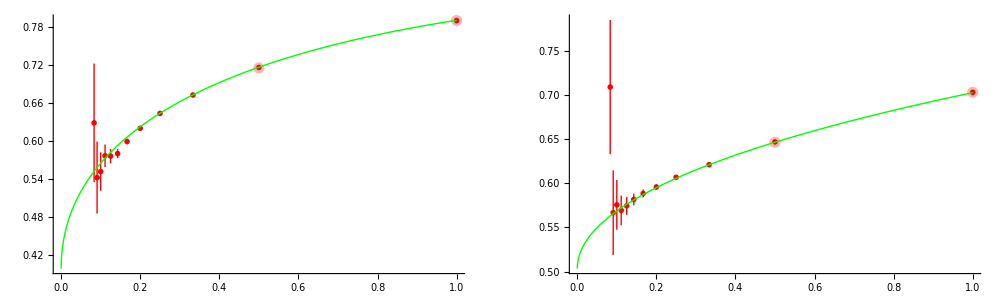

Mean NFactor is 9834.43 with 243 data points

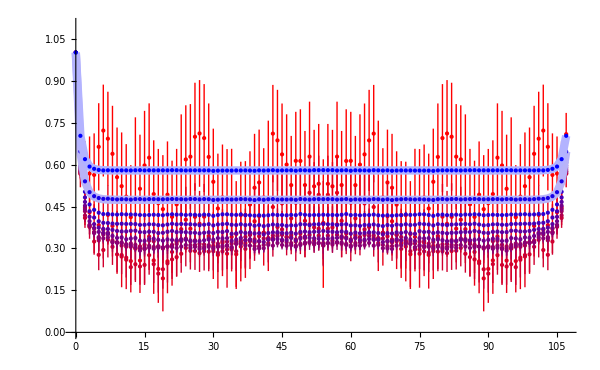

Importing the scalar data from G:\LAT\sd_metropolis\data\pcm_wc_mspace\\scalars_d2_t24_s108_l3.0120.dat

Gx = 0.401815 +/- 0.00843995, NFactor = 9946.63

Link = 0.518908 +/- 0.0103974, NFactor = 9959.26

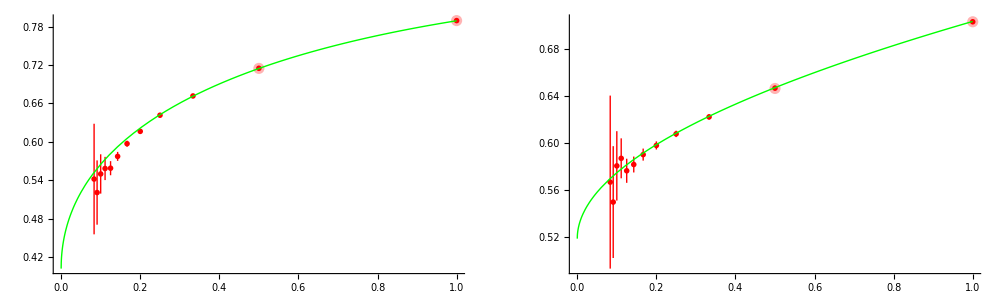

Mean NFactor is 9952.95 with 228 data points

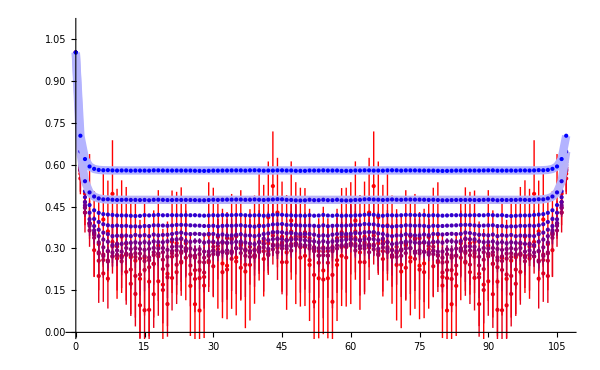

Importing the scalar data from G:\LAT\sd_metropolis\data\pcm_wc_mspace\\scalars_d2_t28_s108_l3.0120.dat

Gx = 0.408566 +/- 0.0080174, NFactor = 9803.41

Link = 0.52222 +/- 0.00906086, NFactor = 9821.11

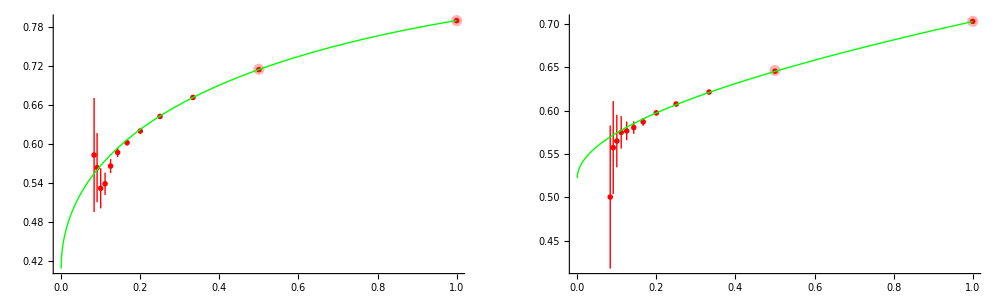

Mean NFactor is 9812.26 with 228 data points

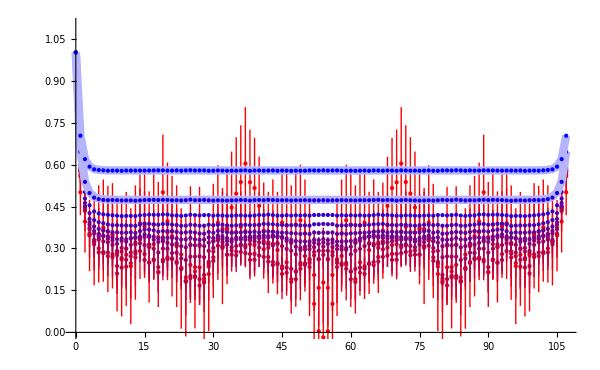

Importing the scalar data from G:\LAT\sd_metropolis\data\pcm_wc_mspace\\scalars_d2_t32_s108_l3.0120.dat

Gx = 0.407973 +/- 0.00789796, NFactor = 9877.91

Link = 0.516678 +/- 0.00959904, NFactor = 9903.36

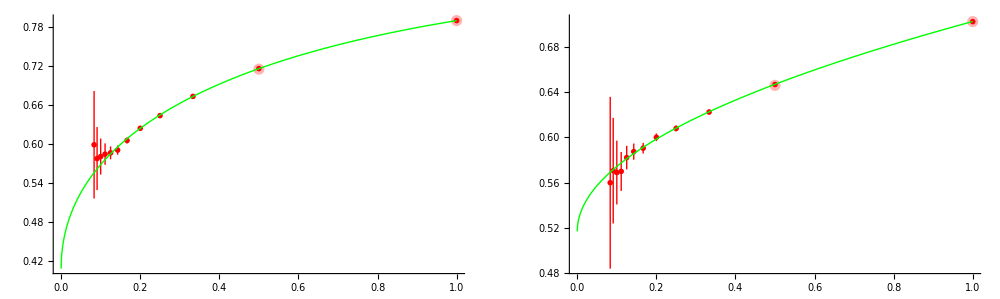

Mean NFactor is 9890.64 with 241 data points

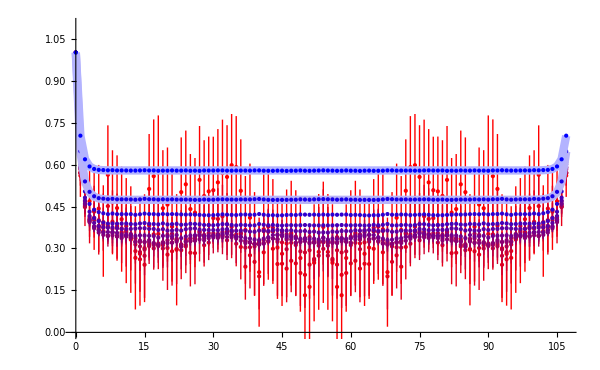

Importing the scalar data from G:\LAT\sd_metropolis\data\pcm_wc_mspace\\scalars_d2_t34_s108_l3.0120.dat

Gx = 0.409098 +/- 0.00762565, NFactor = 9874.8

Link = 0.53043 +/- 0.00950844, NFactor = 9906.24

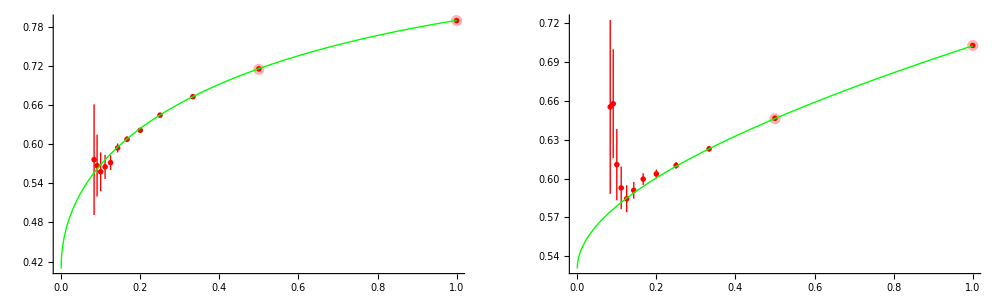

Mean NFactor is 9890.52 with 241 data points

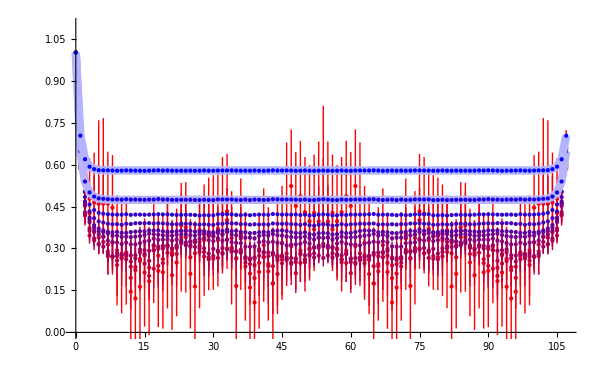

Importing the scalar data from G:\LAT\sd_metropolis\data\pcm_wc_mspace\\scalars_d2_t36_s108_l3.0120.dat

Gx = 0.408354 +/- 0.00792205, NFactor = 9961.04

Link = 0.495565 +/- 0.00964921, NFactor = 9990.63

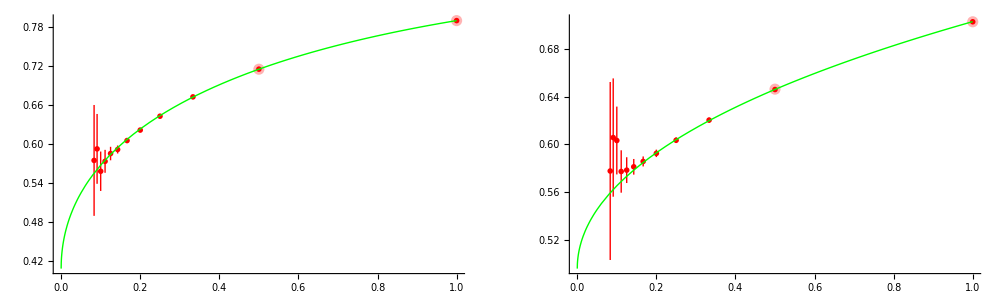

Mean NFactor is 9975.84 with 234 data points

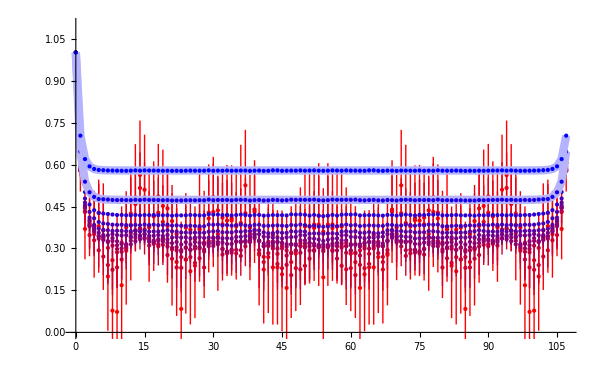

Importing the scalar data from G:\LAT\sd_metropolis\data\pcm_wc_mspace\\scalars_d2_t38_s108_l3.0120.dat

Gx = 0.400255 +/- 0.00900713, NFactor = 9929.43

Link = 0.505599 +/- 0.00903753, NFactor = 9928.6

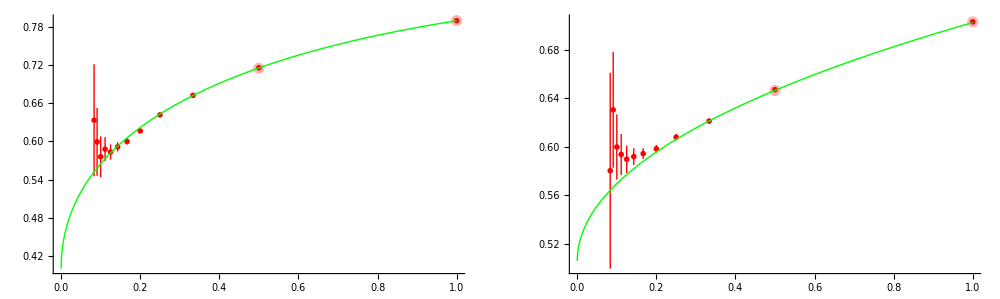

Mean NFactor is 9929.02 with 232 data points

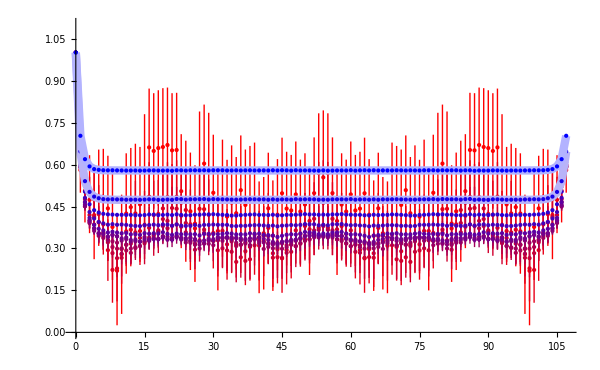

Importing the scalar data from G:\LAT\sd_metropolis\data\pcm_wc_mspace\\scalars_d2_t40_s108_l3.0120.dat

Gx = 0.409475 +/- 0.00852509, NFactor = 9828.15

Link = 0.523385 +/- 0.00995944, NFactor = 9841.95

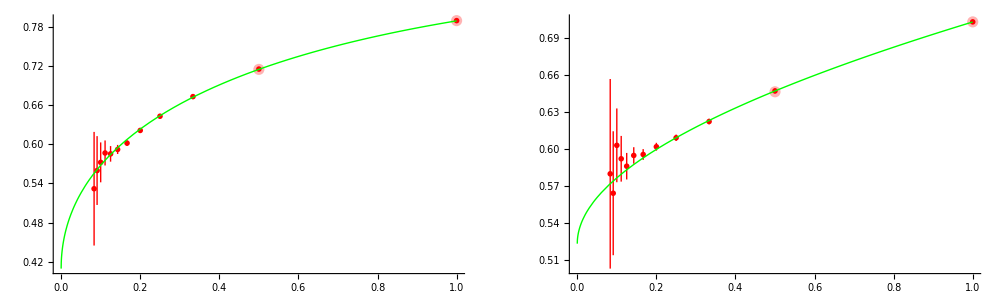

Mean NFactor is 9835.05 with 234 data points

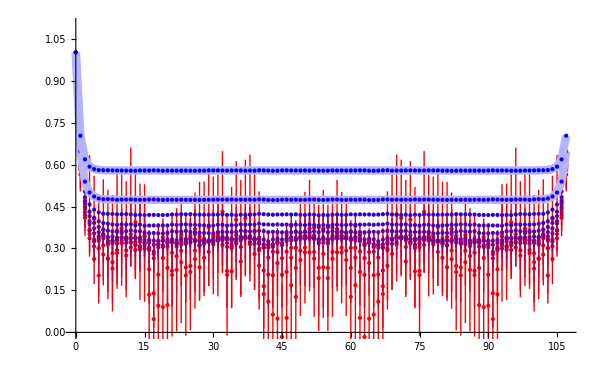

Importing the scalar data from G:\LAT\sd_metropolis\data\pcm_wc_mspace\\scalars_d2_t42_s108_l3.0120.dat

Gx = 0.409833 +/- 0.00729405, NFactor = 9942.73

Link = 0.50005 +/- 0.00884493, NFactor = 9942.03

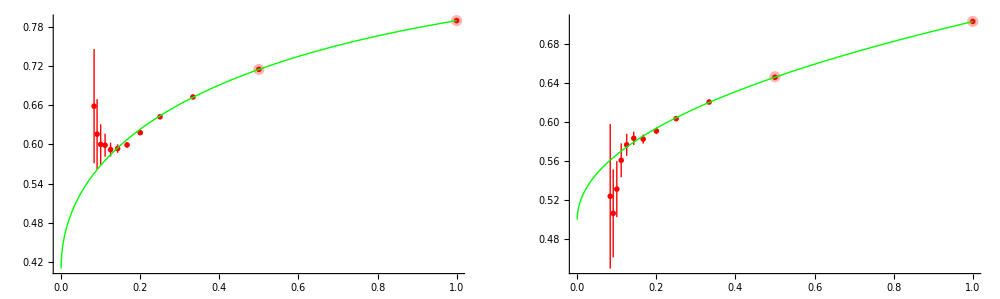

Mean NFactor is 9942.38 with 235 data points

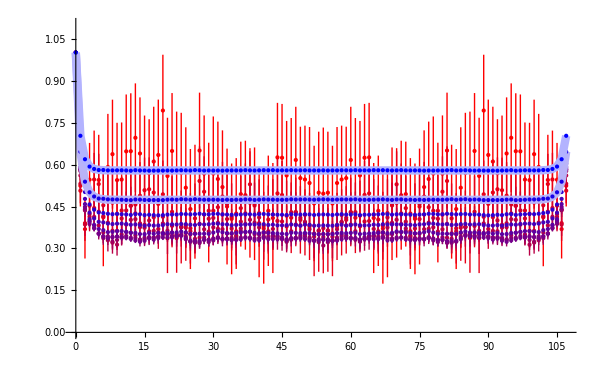

Importing the scalar data from G:\LAT\sd_metropolis\data\pcm_wc_mspace\\scalars_d2_t48_s108_l3.0120.dat

Gx = 0.396138 +/- 0.00771176, NFactor = 9816.18

Link = 0.508579 +/- 0.00919574, NFactor = 9804.54

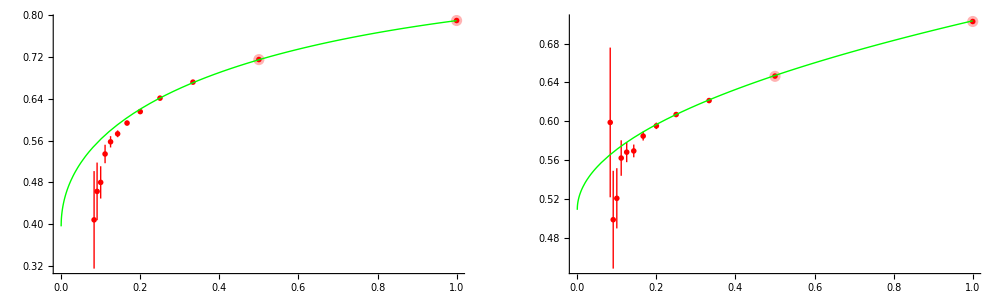

Mean NFactor is 9810.36 with 239 data points

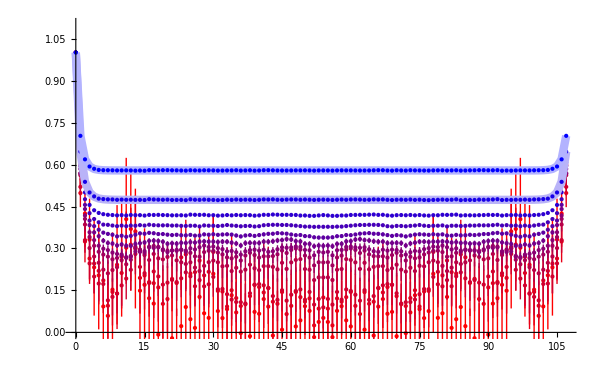

Importing the scalar data from G:\LAT\sd_metropolis\data\pcm_wc_mspace\\scalars_d2_t54_s108_l3.0120.dat

Gx = 0.402427 +/- 0.00817573, NFactor = 9905.52

Link = 0.509484 +/- 0.00950053, NFactor = 9892.07

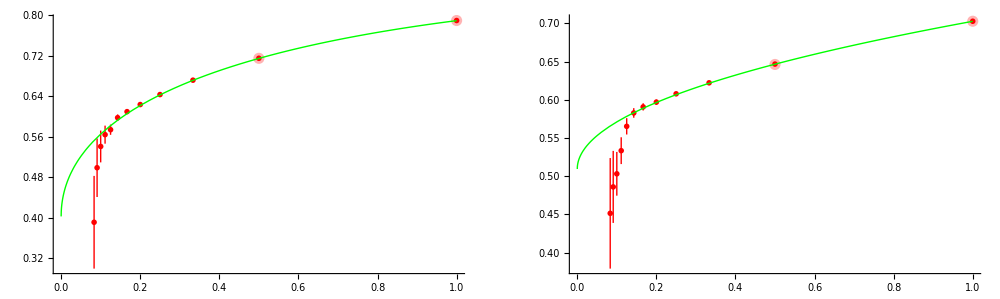

Mean NFactor is 9898.79 with 232 data points

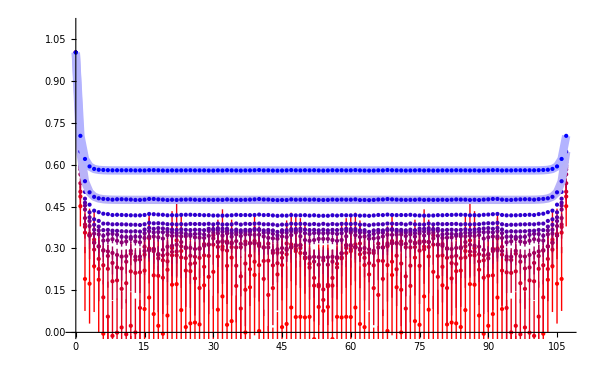

Importing the scalar data from G:\LAT\sd_metropolis\data\pcm_wc_mspace\\scalars_d2_t60_s108_l3.0120.dat

Gx = 0.411339 +/- 0.00814326, NFactor = 9879.97

Link = 0.518175 +/- 0.0100134, NFactor = 9898.85

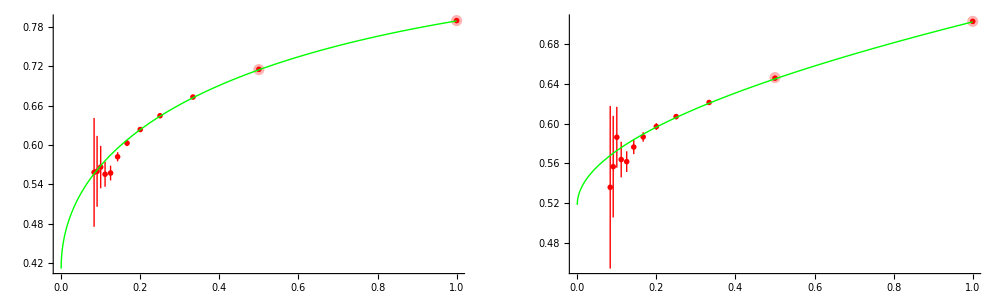

Mean NFactor is 9889.41 with 231 data points

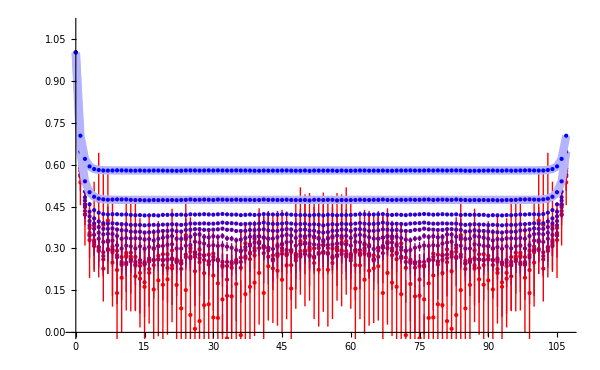

Importing the scalar data from G:\LAT\sd_metropolis\data\pcm_wc_mspace\\scalars_d2_t66_s108_l3.0120.dat

Gx = 0.393883 +/- 0.00918024, NFactor = 9964.4

Link = 0.501372 +/- 0.010013, NFactor = 9938.37

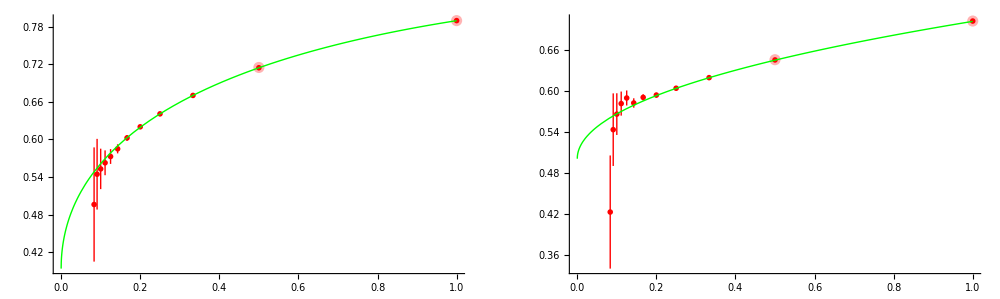

Mean NFactor is 9951.39 with 232 data points

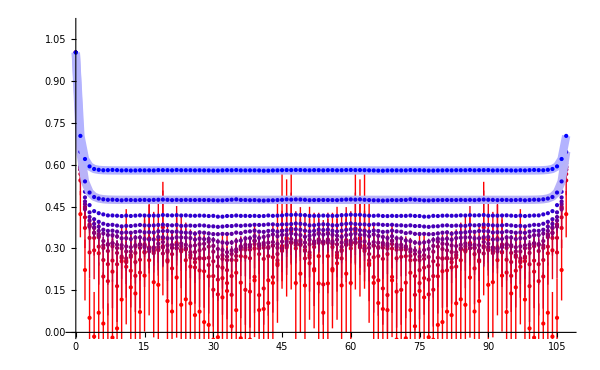

Importing the scalar data from G:\LAT\sd_metropolis\data\pcm_wc_mspace\\scalars_d2_t72_s108_l3.0120.dat

Gx = 0.414087 +/- 0.00779544, NFactor = 9931.89

Link = 0.524232 +/- 0.00938767, NFactor = 9929.36

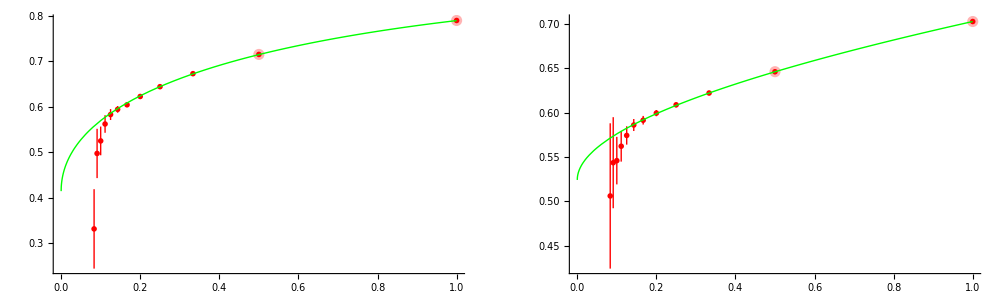

Mean NFactor is 9930.62 with 228 data points

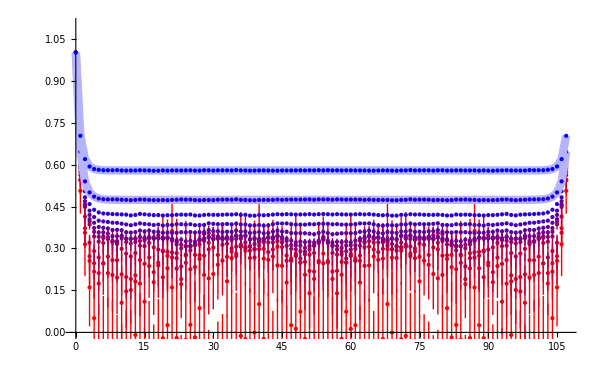

Importing the scalar data from G:\LAT\sd_metropolis\data\pcm_wc_mspace\\scalars_d2_t90_s108_l3.0120.dat

Gx = 0.391498 +/- 0.00816709, NFactor = 9905.32

Link = 0.505406 +/- 0.00966988, NFactor = 9906.99

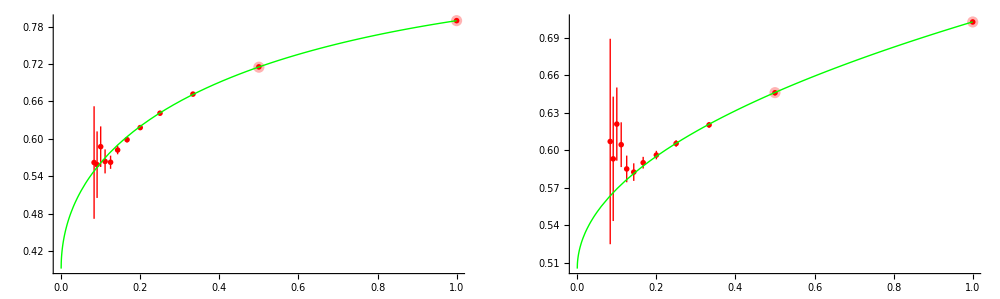

Mean NFactor is 9906.16 with 229 data points

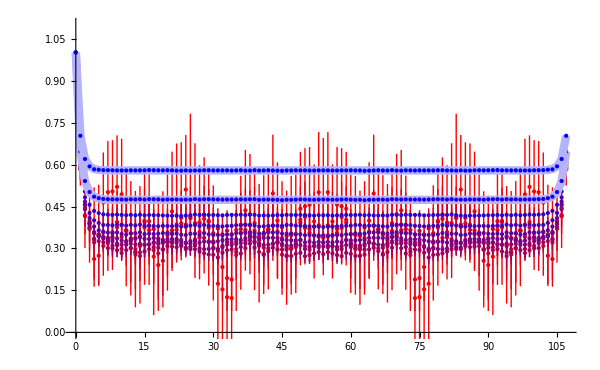

Importing the scalar data from G:\LAT\sd_metropolis\data\pcm_wc_mspace\\scalars_d2_t108_s108_l3.0120.dat

Gx = 0.380158 +/- 0.00821115, NFactor = 9893.86

Link = 0.510908 +/- 0.00779736, NFactor = 9879.39

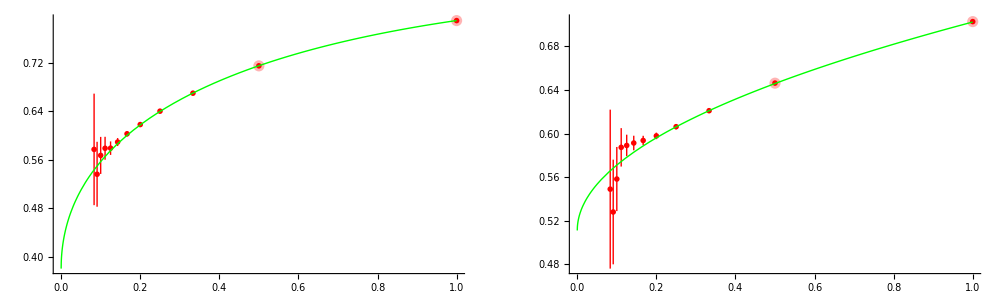

Mean NFactor is 9886.62 with 238 data points

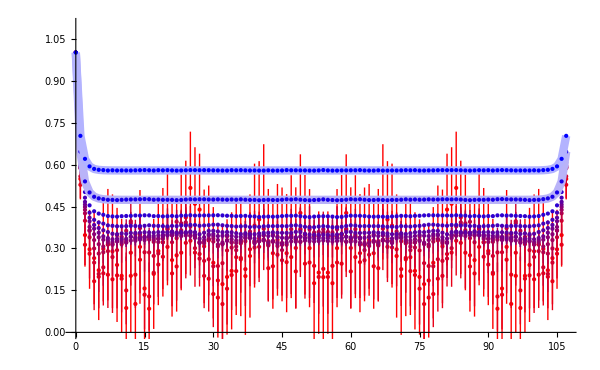

(0.503371 | 0.518908 | 0.52222 | 0.516678 | 0.53043 | 0.495565 | 0.505599 | 0.523385 | 0.50005 | 0.508579 | 0.509484 | 0.518175 | 0.501372 | 0.524232 | 0.505406 | 0.510908
0.00847962 | 0.0103974 | 0.00906086 | 0.00959904 | 0.00950844 | 0.00964921 | 0.00903753 | 0.00995944 | 0.00884493 | 0.00919574 | 0.00950053 | 0.0100134 | 0.010013 | 0.00938767 | 0.00966988 | 0.00779736)

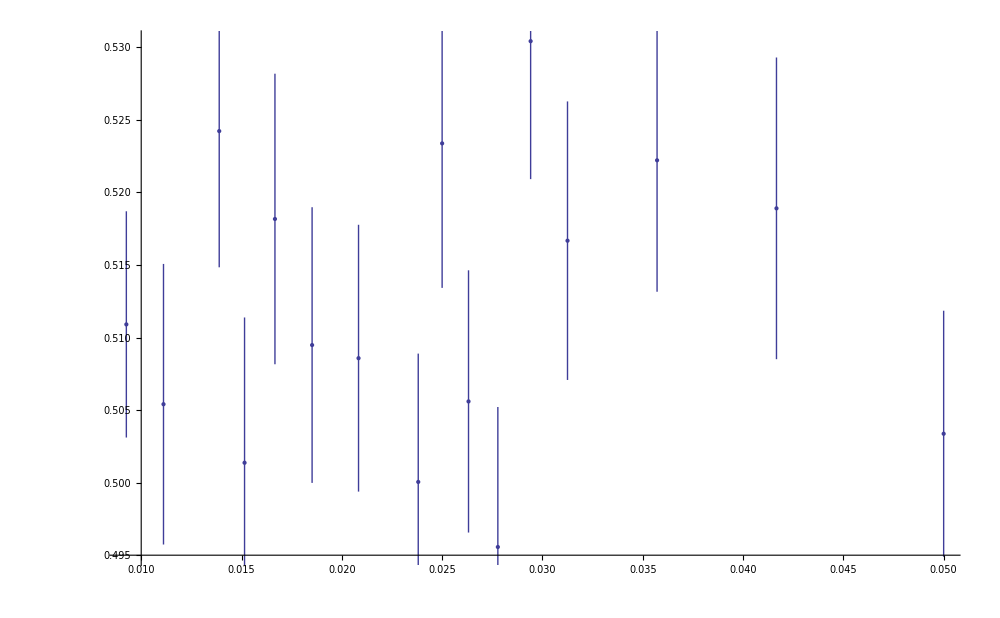

###################################################################################################################

Importing the scalar data from G:\LAT\sd_metropolis\data\pcm_wc_mspace\\scalars_d2_t108_s108_l5.0000.dat

Gx = 0.105939 +/- 0.0627146, NFactor = 63355.3

Link = 0.164309 +/- 0.0813887, NFactor = 63191.1

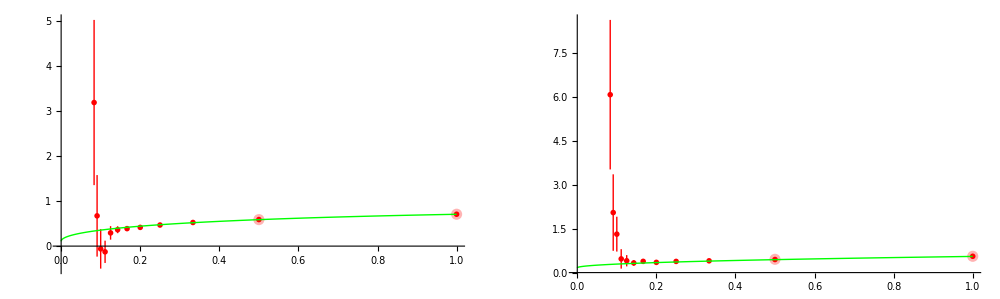

Mean NFactor is 63273.2 with 112 data points

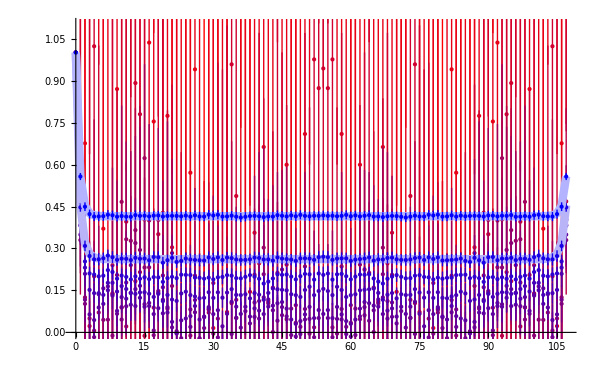

Importing the scalar data from G:\LAT\sd_metropolis\data\pcm_wc_mspace\\scalars_d2_t108_s108_l4.0000.dat

Gx = 0.163058 +/- 0.0331386, NFactor = 27567.2

Link = 0.303052 +/- 0.0489222, NFactor = 27604.1

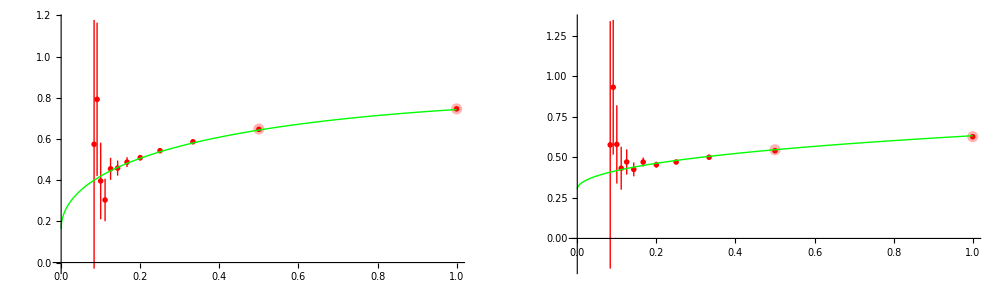

Mean NFactor is 27585.6 with 83 data points

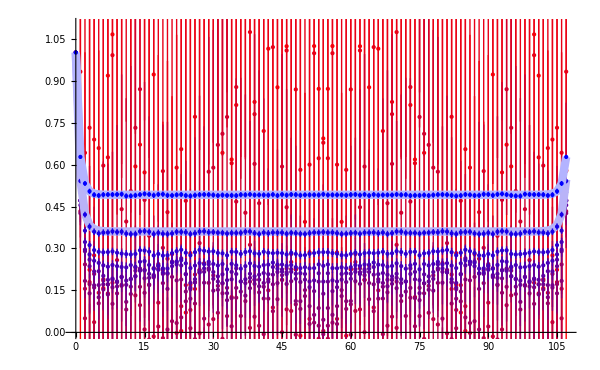

Importing the scalar data from G:\LAT\sd_metropolis\data\pcm_wc_mspace\\scalars_d2_t108_s108_l3.5700.dat

Gx = 0.296587 +/- 0.0212163, NFactor = 17750.5

Link = 0.38568 +/- 0.0298672, NFactor = 17682.3

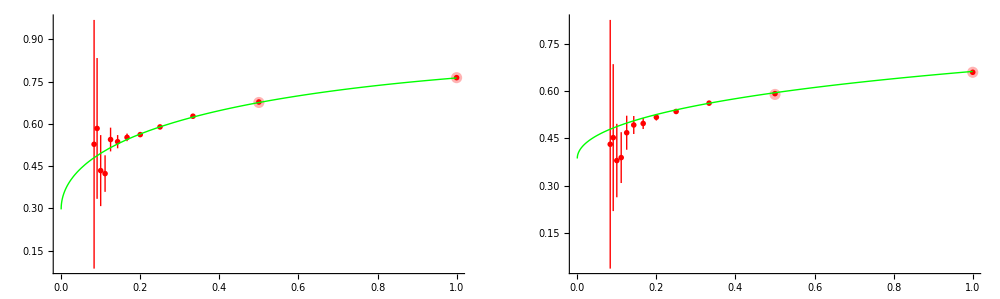

Mean NFactor is 17716.4 with 74 data points

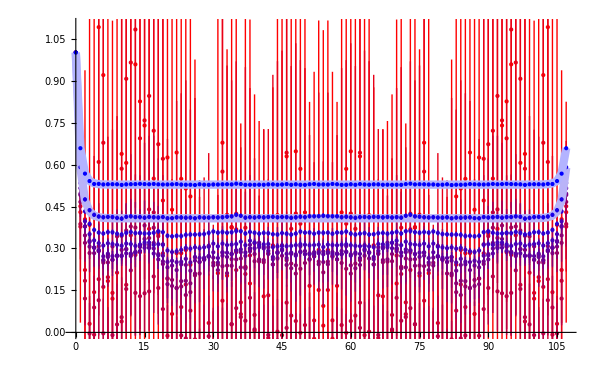

Importing the scalar data from G:\LAT\sd_metropolis\data\pcm_wc_mspace\\scalars_d2_t108_s108_l3.4500.dat

Gx = 0.313445 +/- 0.0231457, NFactor = 16224.9

Link = 0.410874 +/- 0.0294411, NFactor = 16210.7

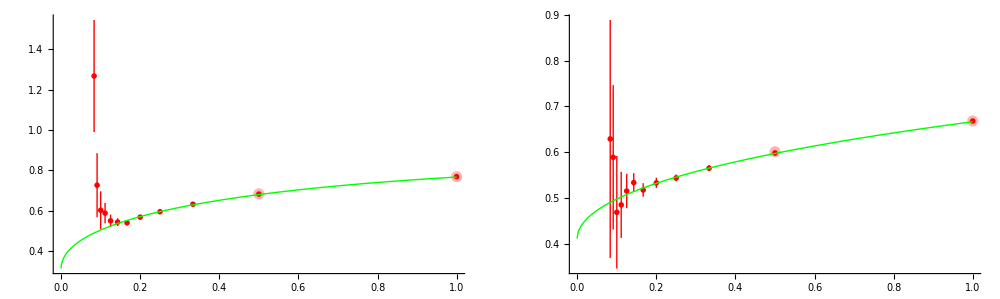

Mean NFactor is 16217.8 with 68 data points

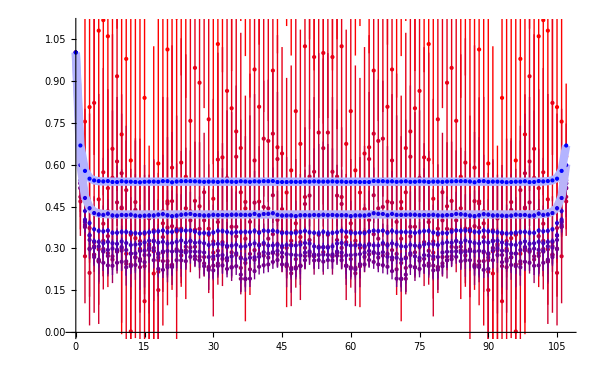

Importing the scalar data from G:\LAT\sd_metropolis\data\pcm_wc_mspace\\scalars_d2_t108_s108_l3.3300.dat

Gx = 0.295733 +/- 0.0211565, NFactor = 14311.4

Link = 0.407572 +/- 0.0245385, NFactor = 14402.9

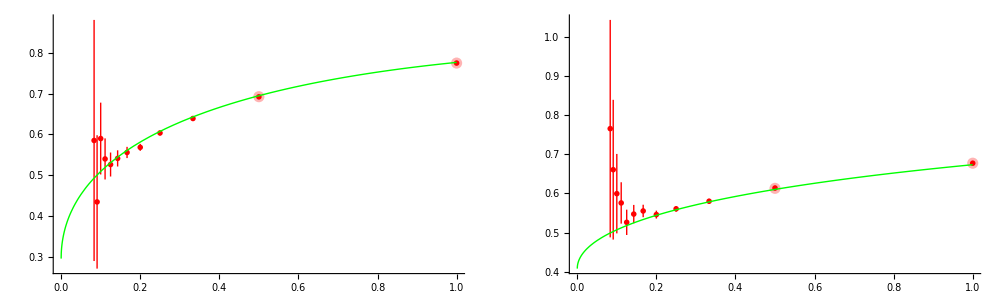

Mean NFactor is 14357.1 with 65 data points

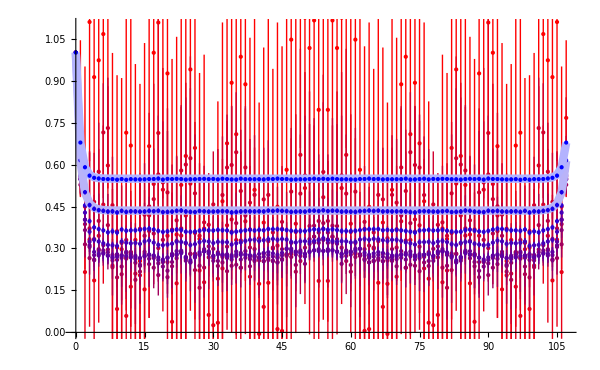

Importing the scalar data from G:\LAT\sd_metropolis\data\pcm_wc_mspace\\scalars_d2_t108_s108_l3.2300.dat

Gx = 0.375146 +/- 0.0170755, NFactor = 12575.8

Link = 0.486243 +/- 0.0230839, NFactor = 12630.1

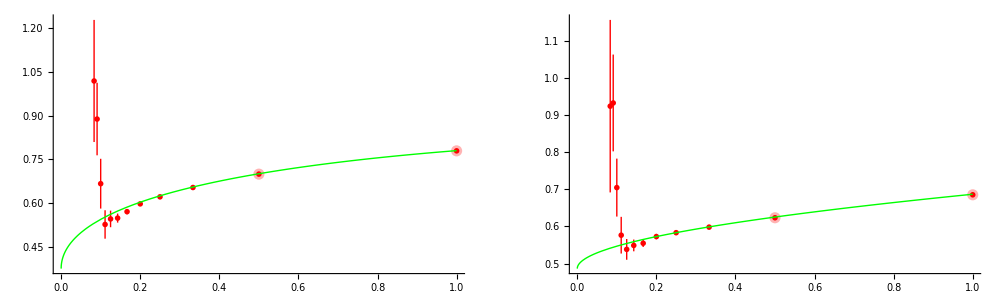

Mean NFactor is 12602.9 with 61 data points

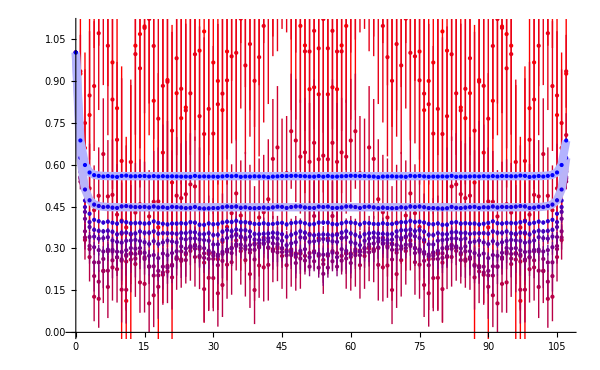

(0.164309 | 0.303052 | 0.38568 | 0.410874 | 0.407572 | 0.486243
0.0813887 | 0.0489222 | 0.0298672 | 0.0294411 | 0.0245385 | 0.0230839)

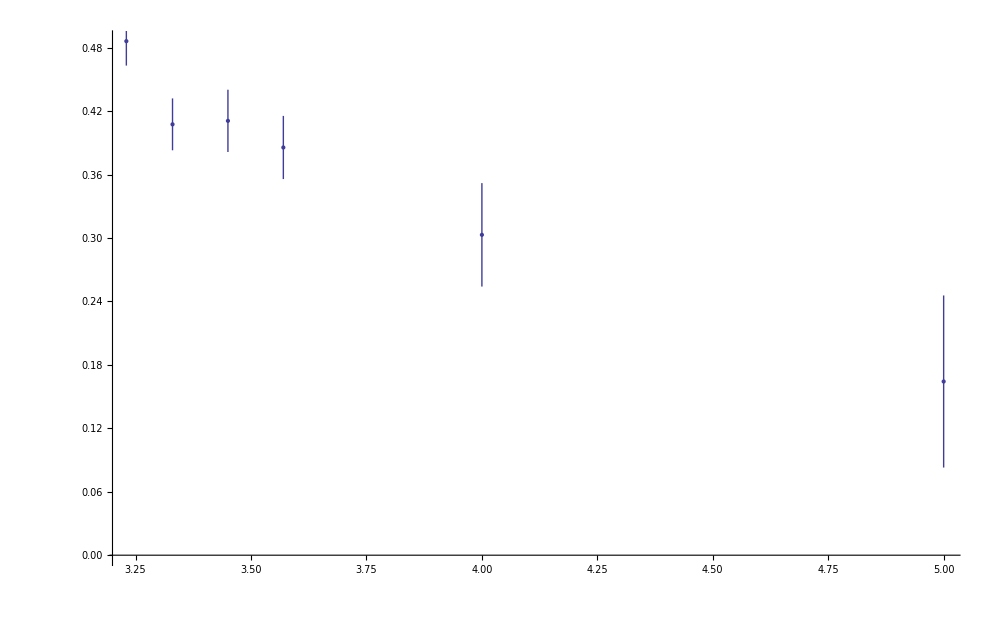

```mathematica
(* Defining the finite T dataset *)
LTs={20,24,28,32,34,36,38,40,42,48,54,60,66,72,90,108};
TemperatureParameterSet=Table[{LT,108,3.0120,11},{LT,LTs}];
(* Defining the coupling dataset *)
λs={5.0,4.0,3.57,3.45,3.33,3.23};
CouplingParameterSet=Table[{108,108,λ,11},{λ,λs}];
(* First updating the data *)
(*Run["ssh-pageant rsync -v -z di72kov@lxlogin5.lrz.de:/home/hpc/b3101/di72kov/sd_metropolis/data/pcm_wc_mspace/*.dat /g/LAT/sd_metropolis/data/pcm_wc_mspace"];*)
TemperatureRes=ScanDataset[TemperatureParameterSet,"G:\\LAT\\sd_metropolis\\data\\pcm_wc_mspace\\",1,{1,2}];
Print[MatrixForm[TemperatureRes]];
PlotWithErrors[1/LTs,TemperatureRes[[1]],TemperatureRes[[2]]]
Print["###################################################################################################################"];
CouplingRes=ScanDataset[CouplingParameterSet,"G:\\LAT\\sd_metropolis\\data\\pcm_wc_mspace\\",1,{1,2}];
Print[MatrixForm[CouplingRes]];
PlotWithErrors[λs,CouplingRes[[1]],CouplingRes[[2]]]
```